```mathematica
getTallyFromClipboard[]:=Module[{eList,nList,errList,toPlot},{eList,nList,errList}=Transpose[ImportString[ NotebookGet[ClipboardNotebook[]][[1,1,1]],"Table"]];toPlot = Transpose[{10^6 Drop[eList,-1],Drop[nList,1]}];{eList,nList,errList,toPlot}]
```

```mathematica
myLinearHist[tally_,title_]:=Module[{eList,nList,errList,toPlot},{eList,nList,errList,toPlot}=tally;ListStepPlot[toPlot,PlotRange->{xRange,yRange},
AxesLabel->{"eV","(n/cm^2)/src"},Filling->Axis,PlotLabel->title<>"
Total = "<>ToString[Total[nList],TraditionalForm]<>"(n/cm^2)/src"]]
```

```mathematica
myCaptureHist[tally_,title_]:=Module[{eList,nList,errList,toPlot},{eList,nList,errList,toPlot}=tally;ListStepPlot[toPlot,PlotRange->{xRange,yRange},
AxesLabel->{"eV","captures/src"},Filling->Axis,PlotLabel->title<>"
Total = "<>ToString[Total[nList],TraditionalForm]<>" captures/src"]]
```

```mathematica
myLogHist[tally_,title_]:=Module[{eList,nList,errList,toPlot},{eList,nList,errList,toPlot}=tally;ListStepPlot[toPlot,PlotRange->{xRange,yRange},ScalingFunctions->{"Log10"},
AxesLabel->{"eV","(n/cm^2)/src"},Ticks->{myTicks,Automatic},Filling->Axis,PlotLabel->title<>"
Total = "<>ToString[Total[nList],TraditionalForm]<>"(n/cm^2)/src"]]
```

```mathematica
getCsvTallyFromClipboard[]:=Module[{eList,nList,errList,toPlot},{eList,nList}=Transpose[ImportString[ NotebookGet[ClipboardNotebook[]][[1,1,1]],"CSV"]];toPlot = Transpose[{Drop[eList,-1],Drop[nList,1]}];{eList,nList,errList,toPlot}]
```

```mathematica
gmLinearHist[tally_]:=Module[{eList,nList,errList,toPlot},{eList,nList,errList,toPlot}=tally;ListStepPlot[toPlot,PlotRange->{xRange,yRange},
AxesLabel->{"eV","(n/cm^2)/src"},Filling->Axis,PlotStyle->Red]]
```

```mathematica
gmLogHist[tally_]:=Module[{eList,nList,errList,toPlot},{eList,nList,errList,toPlot}=tally;ListStepPlot[toPlot,PlotRange->{xRange,yRange},ScalingFunctions->{"Log10"},
AxesLabel->{"eV","(n/cm^2)/src"},Ticks->{myTicks,Automatic},Filling->Axis,PlotStyle->Red]]
```

```mathematica
xRange=Automatic;yRange=Automatic;
```

```mathematica
0.148605 0.93 (* H density in Paraffin *)
```

0.138203

```mathematica
0.851395 0.93 (* C density in Paraffin *)
```

0.791797

```mathematica
tally0874=getTallyFromClipboard[];
```

```mathematica
xRange={0,2.5*^6};
```

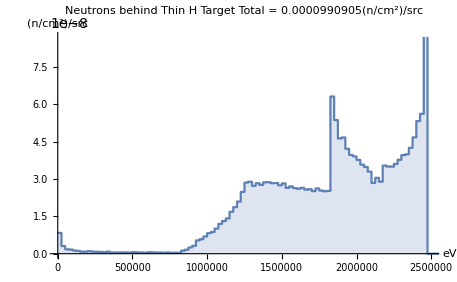

```mathematica
myLinearHist[tally0874,"Neutrons behind Thin H Target"]
```

```mathematica
Total[Take[tally0874[[2]],99]]
```

1.84449×10^-6

```mathematica
tally0874[[2,{99,100,101}]]
```

{5.61755×10^-8,0.000097246,0.}

```mathematica
tally0974=getTallyFromClipboard[];
```

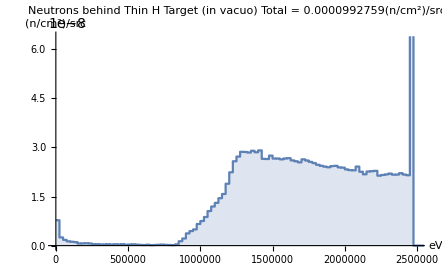

```mathematica
myLinearHist[tally0974,"Neutrons behind Thin H Target (in vacuo)"]
```

```mathematica
{tally0874[[2,2]],tally0974[[2,2]],tally1074[[2,2]]}
```

{8.32778×10^-9,7.75839×10^-9,2.09191×10^-9}

```mathematica
tally1074=getTallyFromClipboard[];
```

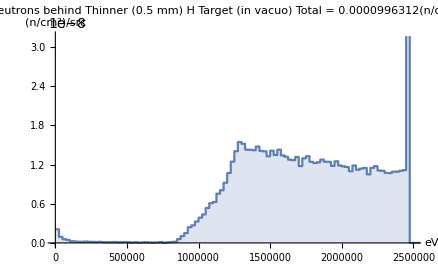

```mathematica
myLinearHist[tally1074,"Neutrons behind Thinner (0.5 mm) H Target (in vacuo)"]
```

```mathematica
(4/3)*Pi*1000^3-(1/40)*100*100-2*100*100-2*100*100 // N
```

4.18875×10^9

```mathematica
tally1174=getTallyFromClipboard[];
```

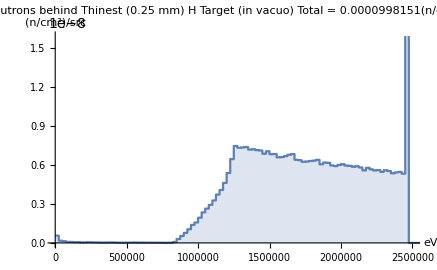

```mathematica
hist1=myLinearHist[tally1174,"Neutrons behind Thinest (0.25 mm) H Target (in vacuo)"]
```

```mathematica
tally11174=getTallyFromClipboard[];
```

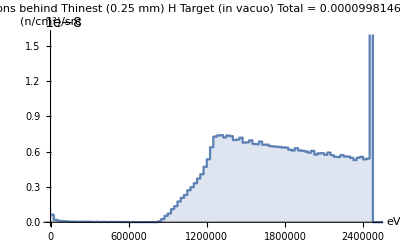

```mathematica
myLinearHist[tally11174,"Neutrons behind Thinest (0.25 mm) H Target (in vacuo)"]
```

```mathematica
phi=(mn+mp)^2/(4 E0 mn mp)dd/V cs rho td (2 mn)/(√(E1/E0)(mn+mp)+√(E0/E1)(mn-mp))deltaE
```

(cs dd deltaE (mn+mp)^2 rho td)/(2 E0 mp (√(E0/E1) (mn-mp)+√(E1/E0) (mn+mp)) V)

```mathematica
csElasticH=Interpolation[ImportString["2.00000000e+00      2.90838e+00
2.20000000e+00      2.75345e+00
2.40000000e+00      2.61697e+00
2.60000000e+00      2.49537e+00
2.80000000e+00      2.38600e+00
3.00000000e+00      2.28686e+00
3.20000000e+00      2.19638e+00","Table"]];
```

```mathematica
csElasticH[2.451]
```

2.58465

```mathematica
phiSubs={cs->2.58465,dd->2,rho->0.082572,td->1/40,E0->2.451*^6,mp->938.272,mn->939.565,V->2 100 100,deltaE->0.025*^6}
```

{cs→2.58465,dd→2,rho→0.082572,td→1/40,E0→2.451×10^6,mp→938.272,mn→939.565,V→20000,deltaE→25000.}

```mathematica
phi/.phiSubs
```

(1.02265×10^-11)/(2024.28 √(1/E1)+1.19946 √E1)

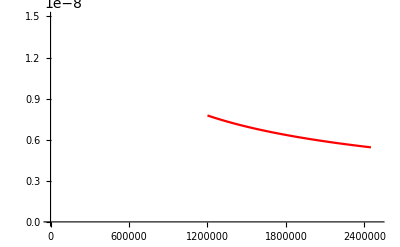

```mathematica
ptheory=Plot[phi/.phiSubs,{E1,1.2*^6,2.45*^6},PlotRange->{{0,2.5*^6},{0,1.5*^-8}},PlotStyle->Red]
```

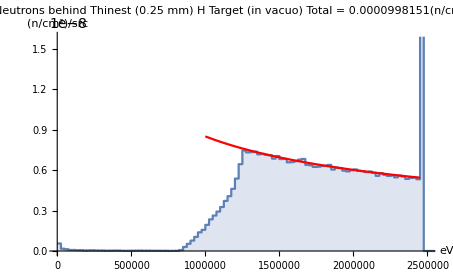

```mathematica
Show[hist1,ptheory]
```

```mathematica
csElasticC=Interpolation[ImportString["2.20000000e+00      1.65433e+00
2.22000000e+00      1.64507e+00
2.24000000e+00      1.63723e+00
2.26000000e+00      1.63050e+00
2.28000000e+00      1.62472e+00
2.30000000e+00      1.61978e+00
2.32000000e+00      1.61566e+00
2.34000000e+00      1.61234e+00
2.36000000e+00      1.60983e+00
2.38000000e+00      1.60814e+00
2.40000000e+00      1.60731e+00
2.42000000e+00      1.60738e+00
2.44000000e+00      1.60841e+00
2.46000000e+00      1.61046e+00
2.48000000e+00      1.61361e+00
2.50000000e+00      1.61794e+00
2.52000000e+00      1.62356e+00
2.54000000e+00      1.63059e+00
2.56000000e+00      1.63916e+00
2.58000000e+00      1.64944e+00
2.60000000e+00      1.66163e+00
2.62000000e+00      1.67595e+00
2.64000000e+00      1.69270e+00
2.66000000e+00      1.71220e+00
2.68000000e+00      1.73490e+00
2.70000000e+00      1.76133e+00
2.72000000e+00      1.79221e+00
2.74000000e+00      1.82850e+00
2.76000000e+00      1.87157e+00
2.78000000e+00      1.92375e+00
2.80000000e+00      1.99427e+00
2.80200000e+00      2.00452e+00
2.80400000e+00      2.01669e+00
2.80600000e+00      2.03228e+00
2.80800000e+00      2.05473e+00
2.81000000e+00      2.09341e+00","Table"]];
```

```mathematica
csElasticC[2.451]
```

1.60941

```mathematica
phiSubsC={cs->1.60941,dd->2,rho->0.039701,td->1/40,E0->2.451*^6,mp->11.89691424  939.565,mn->939.565,V->2 100 100,deltaE->0.025*^6}
```

{cs→1.60941,dd→2,rho→0.039701,td→1/40,E0→2.451×10^6,mp→11177.9,mn→939.565,V→20000,deltaE→25000.}

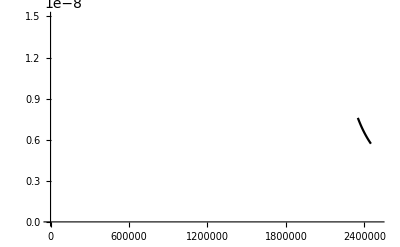

```mathematica
ptheoryC=Plot[phi/.phiSubsC,{E1,2.35*^6,2.45*^6},PlotRange->{{0,2.5*^6},{0,1.5*^-8}},PlotStyle->Black]
```

```mathematica
tally1274=getTallyFromClipboard[];
```

```mathematica
yRange={0,1.3*^-8};
```

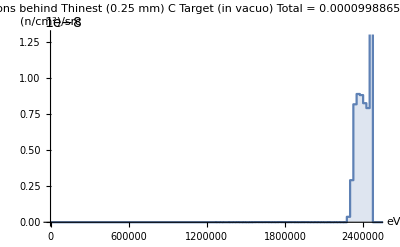

```mathematica
hist1274=myLinearHist[tally1274,"Neutrons behind Thinest (0.25 mm) C Target (in vacuo)"]
```

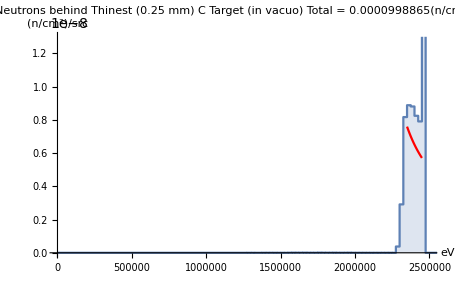

```mathematica
Show[hist1274,ptheoryC]
```

```mathematica
tally1374=getTallyFromClipboard[];
```

```mathematica
yRange={0,1.9*^-8};
```

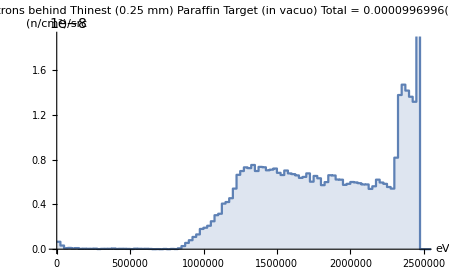

```mathematica
hist1374=myLinearHist[tally1374,"Neutrons behind Thinest (0.25 mm) Paraffin Target (in vacuo)"]
```

```mathematica
tally1474=getTallyFromClipboard[];
```

```mathematica
yRange={0,6*^-8};
```

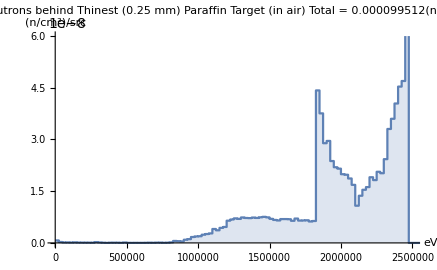

```mathematica
hist1474=myLinearHist[tally1474,"Neutrons behind Thinest (0.25 mm) Paraffin Target (in air)"]
```

```mathematica
(4/3)*Pi*1000^3-25*100*100-2*100*100-2*100*100 // N
```

4.1885×10^9

```mathematica
tally1504=getTallyFromClipboard[];
```

```mathematica
yRange={0,6*^-7};
```

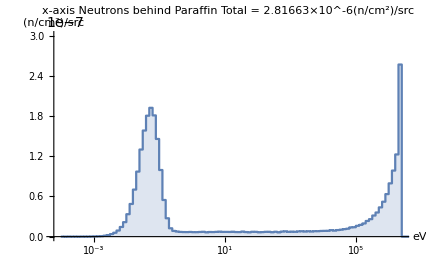

```mathematica
hist1504=myLogHist[tally1504,"x-axis Neutrons behind Paraffin"]
```

```mathematica
tally1544=getTallyFromClipboard[];
```

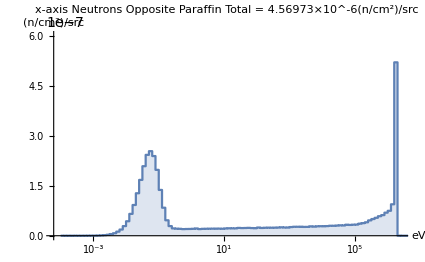

```mathematica
myLogHist[tally1544,"x-axis Neutrons Opposite Paraffin"]
```

```mathematica
tallyGmH=getCsvTallyFromClipboard[];
```

```mathematica
yRange={0,2*^-8};
```

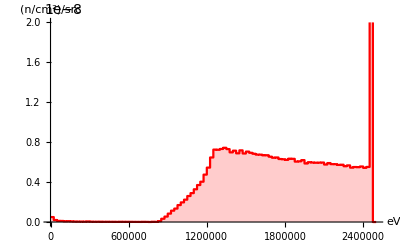

```mathematica
histGmH=gmLinearHist[tallyGmH]
```

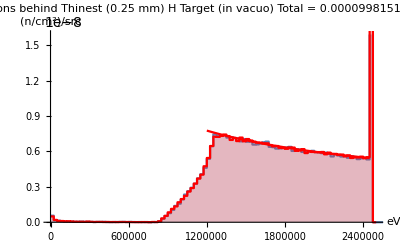

```mathematica
Show[hist1,histGmH,ptheory]
```

```mathematica
tallyGmC=getCsvTallyFromClipboard[];
```

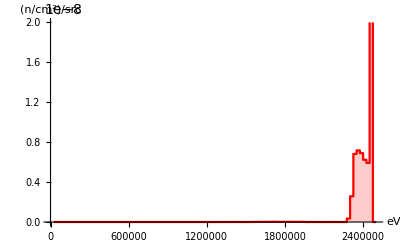

```mathematica
histGmC=gmLinearHist[tallyGmC]
```

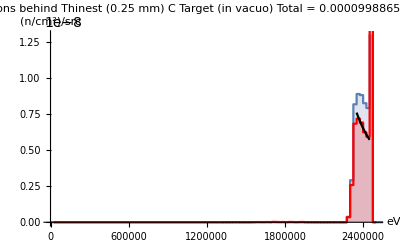

```mathematica
Show[hist1274,histGmC,ptheoryC]
```

```mathematica
tallyGmP=getCsvTallyFromClipboard[];
```

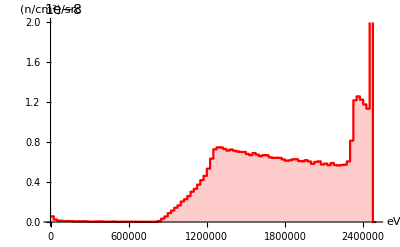

```mathematica
histGmP=gmLinearHist[tallyGmP]
```

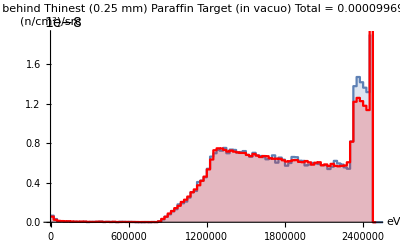

```mathematica
Show[hist1374,histGmP]
```

```mathematica
tallyGmPinAir=getCsvTallyFromClipboard[];
```

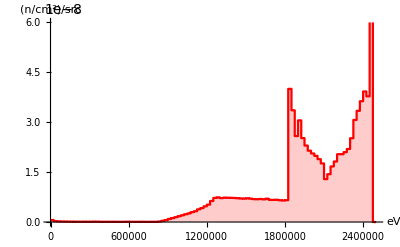

```mathematica
histGmPinAir=gmLinearHist[tallyGmPinAir]
```

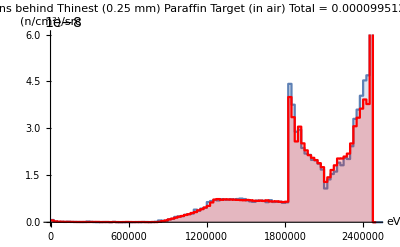

```mathematica
Show[hist1474,histGmPinAir]
```

```mathematica
tallyGmThickP=getCsvTallyFromClipboard[];
```

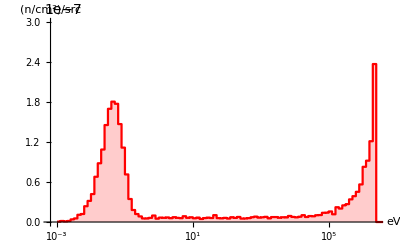

```mathematica
histGmThickP=gmLogHist[tallyGmThickP]
```

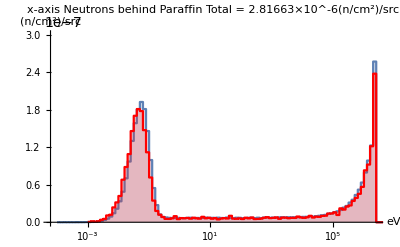

```mathematica
Show[hist1504,histGmThickP]
```

```mathematica
Total[tallyGmThickP[[2]]]
```

2.70687×10^-6

```mathematica
yRange={0,3*^-7};
```

```mathematica
(4/3)*Pi*1000^3-25*100*100-2*100*100-2*100*100 // N
```

4.1885×10^9

```mathematica
tally1604=getTallyFromClipboard[];
```

```mathematica
yRange={0,6*^-7};
```

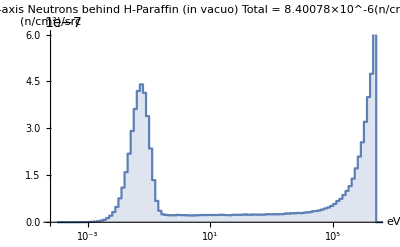

```mathematica
hist1604=myLogHist[tally1604,"x-axis Neutrons behind H-Paraffin (in vacuo)"]
```

```mathematica
tallyGmThickH=getCsvTallyFromClipboard[];
```

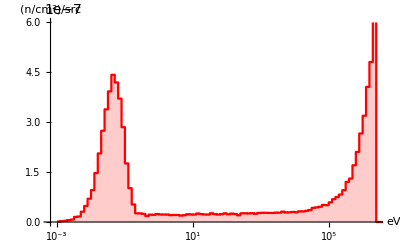

```mathematica
histGmThickH=gmLogHist[tallyGmThickH]
```

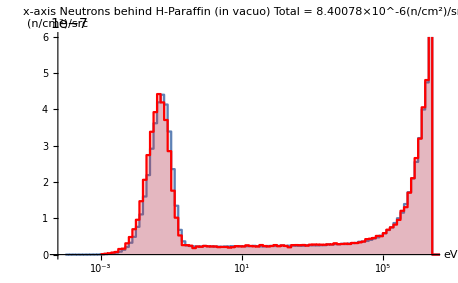

```mathematica
Show[hist1604,histGmThickH]
```

```mathematica
Total[tallyGmThickH[[2]]]
```

8.51459×10^-6

```mathematica
Take[tally1604[[2]] ,-11]
```

{2.55555×10^-7,3.2118×10^-7,3.99982×10^-7,4.74621×10^-7,9.70975×10^-7,0.,0.,0.,0.,0.,0.}

```mathematica
Take[tally1604[[2]] tally1604[[3]],-11]
```

{1.89111×10^-9,2.08767×10^-9,2.2799×10^-9,2.37311×10^-9,3.10712×10^-9,0.,0.,0.,0.,0.,0.}

```mathematica
Take[tallyGmThickH[[2]],-10]
```

{2.6612×10^-7,3.19604×10^-7,4.06043×10^-7,4.81205×10^-7,9.70861×10^-7,0.,0.,0.,0.,0.}

```mathematica
Table[{i,tally1604[[1,i]]},{i,Length[tally1604[[1]]]}]
```

```mathematica
tally1604[[1,36]]
```

3.1623×10^-7

```mathematica
10^6 Total[Take[tally1604[[2]],36]Take[tally1604[[1]],36]]/Total[Take[tally1604[[2]],36]]
```

0.0672577

```mathematica
Total[Take[tallyGmThickH[[2]],26]Take[tallyGmThickH[[1]],26]]/Total[Take[tallyGmThickH[[2]],26]]
```

0.0597219

```mathematica
Out[508]/Out[511]
```

1.12618

```mathematica
%^10
```

3.28157

```mathematica
10^(1/10)//N
```

1.25893

```mathematica
tallyGmThickH[[1,26]]
```

0.3162

```mathematica
tallyGmThickHlinear=getCsvTallyFromClipboard[];
```

```mathematica
xRange={0,0.3}; yRange={0,3.5*^-7};
```

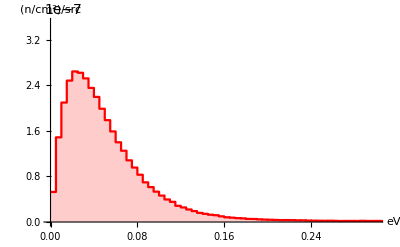

```mathematica
histGmThickHlinear =gmLinearHist[tallyGmThickHlinear]
```

```mathematica
Total[Take[tallyGmThickHlinear[[2]],100](Take[tallyGmThickHlinear[[1]],100]-.0025)]/Total[Take[tallyGmThickHlinear[[2]],100]]
```

0.0584417

```mathematica
tallyGmThickHlinear[[1,61]]
```

0.3

```mathematica
Total[Take[tallyGmThickHlinear[[2]],61](Take[tallyGmThickHlinear[[1]],61]-.0025)]/Total[Take[tallyGmThickHlinear[[2]],61]]
```

0.0534353

```mathematica
tally1704=getTallyFromClipboard[];
```

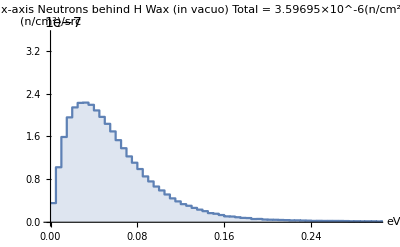

```mathematica
hist1704=myLinearHist[tally1704,"x-axis Neutrons behind H Wax (in vacuo)"]
```

```mathematica
Total[Take[tally1704[[2]],61](10^6 Take[tally1704[[1]],61]-.0025)]/Total[Take[tally1704[[2]],61]]
```

0.0594891

```mathematica
Total[Take[tally1704[[2]],61]]
```

3.47944×10^-6

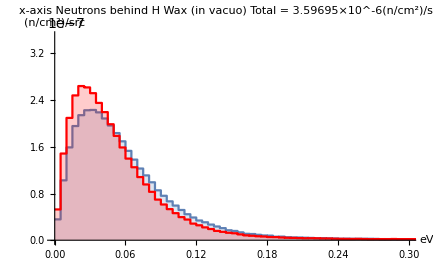

```mathematica
Show[hist1704,histGmThickHlinear]
```

```mathematica
0.99^-1000
```

23163.6

```mathematica
tally1894=getTallyFromClipboard[];
```

```mathematica
yRange={0,0.085};
```

```mathematica
xRange={0,0.2};
```

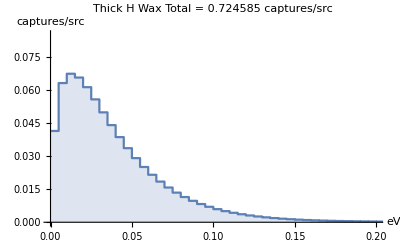

```mathematica
myCaps18=myCaptureHist[tally1894,"Thick H Wax"]
```

```mathematica
0.082572 25 100 100
```

20643.

```mathematica
tally18104=getTallyFromClipboard[];
```

```mathematica
yRange={0,1*^-5};
```

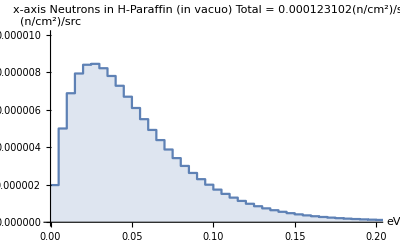

```mathematica
hist18104=myLinearHist[tally18104,"x-axis Neutrons in H-Paraffin (in vacuo)"]
```

```mathematica
tallyGmThickHwax=getCsvTallyFromClipboard[];
```

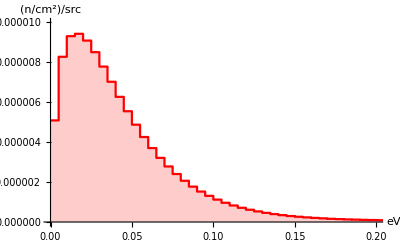

```mathematica
histGmThickHwax=gmLinearHist[tallyGmThickHwax]
```

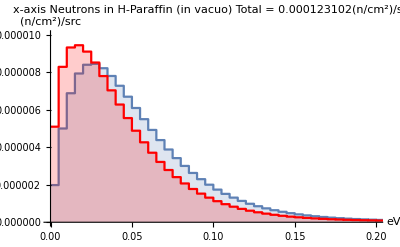

```mathematica
Show[hist18104,histGmThickHwax]
```

```mathematica
gmCapturesThickHwax=getCsvTallyFromClipboard[];
```

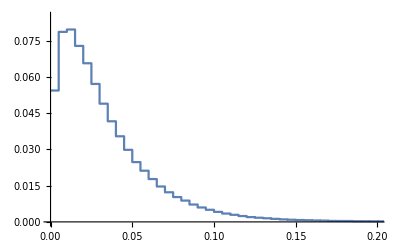

```mathematica
ListStepPlot[gmCapturesThickHwax[[4]],PlotRange->{xRange,yRange}]
```

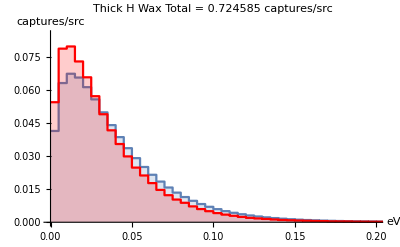

```mathematica
Show[myCaps18,ListStepPlot[gmCapturesThickHwax[[4]],PlotRange->{xRange,yRange},PlotStyle->Red,Filling->Axis]]
```